```mathematica
(*Test to see if window matters (it does not) *)
```

```mathematica
detailIDdr={{AL, AK, AZ, AR, CA, CO, CT, DC, DE,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY},{416468,416471,416484,416491,416498,416505,416508,416623,416511,417861,416514,416520,416523,416532,416542,416545,416554,416557,416560,416569,416584,416593,416599,416602,416612,416619,416487,416490,416496,416502,416516,416526,416529,416534,416539,416548,416551,416590,416595,416605,416608,416611,416617,416632,416636,416639,416642,416645,416648,416653,416654},
{416469,416472,416485,416493,416500,416506,416509,416624,416512,417866,416515,416521,416524,416537,416543,416546,416555,416558,416561,416570,416585,416594,416600,416603,416614,416621,416488,416492,416497,416503,416518,416527,416530,416535,416540,416549,416552,416591,416597,416606,416609,416613,416618,416634,416637,416640,416643,416646,416649,416651,416655}};
```

```mathematica
ev=Import["http://www.electoral-vote.com/evp2008/Pres/Excel/today.csv"];
```

```mathematica
datad=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[2,i]] ]],1],{i,51}];
```

```mathematica
datar=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[3,i]] ]],1],{i,51}];
```

```mathematica
datad[[5,664,2;;-1]]=datad[[5,663,2;;-1]](*data error: CA price on 9.11=3 instead of 91.2*)
```

{91.2,91.2,91.2,91.2,0}

```mathematica
datar[[23,657,2;;-1]]=datar[[23,656,2;;-1]]
```

{38.5,36.2,40,39.9,35}

```mathematica
closed=datad[[All,All,5]];
closer=datar[[All,All,5]];
```

```mathematica
window=45;window1=window+1;
```

```mathematica
returnsd=Table[Log[closed[[i,j-1]]/closed[[i,j]]],{i,51},{j,-window,-1}];
```

```mathematica
returnsr=Table[Log[closer[[i,j-1]]/closer[[i,j]]],{i,51},{j,-window,-1}];
```

```mathematica
chanced=Table[closed[[i,-window1;;-1]]/(closed[[i,-window1;;-1]]+closer[[i,-window1;;-1]]),{i,51}];
```

```mathematica
returnsc=Table[Log[chanced[[i,j-1]]/chanced[[i,j]]],{i,51},{j,-window,-1}];
```

```mathematica
chanced[[All,-1]]//N
```

{0.06,0.06,0.07,0.08,0.931,0.679321,0.91,0.97,0.93,0.44,0.099,0.977,0.03,0.96,0.39,0.795,0.06,0.059,0.09,0.892,0.927,0.963,0.729,0.732,0.07,0.3,0.199,0.025,0.502,0.54,0.886,0.75,0.92,0.435,0.084,0.501,0.033,0.85,0.72,0.95,0.075,0.08,0.05,0.075,0.02,0.925,0.55,0.88,0.169,0.728,0.042}

```mathematica
datad[[1,-window,1]]
```

Aug 14, 2008

```mathematica
winning=Table[Total[Table[If[chanced[[i,-j]]>.5,ev[[2;;-2,2]][[i]],0],{i,51}]],{j,window}]
```

{311,311,291,278,278,273,278,293,293,273,273,273,273,273,273,273,273,273,273,311,311,311,311,311,293,293,293,293,306,293,293,306,306,306,311,306,291,291,306,306,306,306,306,311,311}

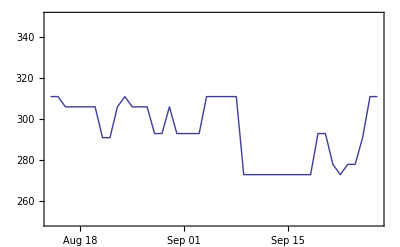

```mathematica
DateListPlot[Reverse[winning],{2008,8,14},Joined->True,PlotRange->{Automatic,{250,350}}]
```

```mathematica
timeleft=DateDifference[DateList[][[1;;3]],{2008,11,4}]
```

38

```mathematica
liquidityd=Table[Count[returnsd[[i,-window;;-1]],n_/;n!=0],{i,51}]
```

{7,10,8,7,17,27,15,1,10,30,27,30,16,11,25,27,12,15,21,16,11,9,24,27,11,28,25,8,33,23,21,27,19,26,15,30,7,22,26,9,12,19,6,14,2,16,29,16,19,25,12}

```mathematica
liquidityr=Table[Count[returnsr[[i,-window;;-1]],n_/;n!=0],{i,51}]
```

{10,15,8,17,22,32,17,21,7,29,21,4,8,7,22,23,22,9,19,17,10,12,30,27,18,31,24,8,31,26,27,26,19,24,14,30,8,23,34,10,11,14,11,17,4,18,29,17,18,26,3}

```mathematica
{Mean[liquidityd],Mean[liquidityr]}//N
```

{17.7059,18.2353}

```mathematica
Needs["Histograms`"]
```

```mathematica
<<MultivariateStatistics`
```

```mathematica
cvard=Table[,{51},{51}];
For[j=1,j≤51,j++,
For[i=1, i≤51, i++, cvard[[j,i]]=Covariance[returnsd[[i]],returnsd[[j]] ]]]
```

```mathematica
cvarr=Table[,{51},{51}];
For[j=1,j≤51,j++,
For[i=1, i≤51, i++, cvarr[[j,i]]=Covariance[returnsr[[i]],returnsr[[j]] ]]]
```

```mathematica
closed=Table[closed[[i,-window;;-1]],{i,51}];
```

```mathematica
closer=Table[closer[[i,-window;;-1]],{i,51}];
```

```mathematica
simsdet=Table[
ds=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvard],timeleft]]];
rs=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvarr],timeleft]]];
endd=closed[[All,-1]];
endr=closer[[All,-1]];
For[j=1,j≤51,j++,Do[endd[[j]]=endd[[j]] ds[[j,i]];endr[[j]]=endr[[j]] rs[[j,i]],{i,timeleft}]];
chanced=endd/(endd+endr);
Table[If[chanced[[i]]>.5,ev[[2;;-2,2]][[i]],0],{i,51}],{5000}
];
```

MultinormalDistribution::sing: Warning: Singular multinormal distribution encountered.

General::stop: Further output of MultinormalDistribution :: "sing" will be suppressed during this calculation.

```mathematica
sims=Map[Total,simsdet];
```

```mathematica
Count[sims,n_/;n>268]/Length[sims]//N
```

0.937

```mathematica
{Mean[sims],StandardDeviation[sims]}//N
```

{307.406,28.1104}

```mathematica
counts=Table[Count[sims,n_/;n==i],{i,538}];
```

```mathematica
counts[[269]]/5000.
```

0.0256

```mathematica
mode=Position[counts,Max[counts]][[1,1]]
```

306

```mathematica
chanced=Table[closed[[i,-window;;-1]]/(closed[[i,-window;;-1]]+closer[[i,-window;;-1]]),{i,51}];today=Total[Table[If[chanced[[i,-1]]>.5,ev[[2;;-2,2]][[i]],0],{i,51}]]
```

311

```mathematica
counts[[today]] ==mode(*Everything breaking exactly like today is the mode of the distribution*)
```

False

```mathematica
hr=Histogram[Select[sims, #<269&],Ticks->{Table[10x,{x,20,38}],None},HistogramCategories->Table[x,{x,538}],BarStyle->Red];
```

```mathematica
hd=Histogram[Select[sims, #>268&],Ticks->{Table[10x,{x,20,38}],None},HistogramCategories->Table[x,{x,538}],BarStyle->Blue];
```

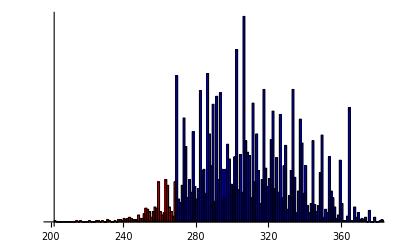

```mathematica
Show[hr,hd,PlotRange->{{200,380},{0,Max[counts]}}]
```

```mathematica
{Table[i,{i,250,310}],Table[Count[sims,n_/;n==i],{i,250,310}]}//MatrixForm//N
```

(250. | 251. | 252. | 253. | 254. | 255. | 256. | 257. | 258. | 259. | 260. | 261. | 262. | 263. | 264. | 265. | 266. | 267. | 268. | 269. | 270. | 271. | 272. | 273. | 274. | 275. | 276. | 277. | 278. | 279. | 280. | 281. | 282. | 283. | 284. | 285. | 286. | 287. | 288. | 289. | 290. | 291. | 292. | 293. | 294. | 295. | 296. | 297. | 298. | 299. | 300. | 301. | 302. | 303. | 304. | 305. | 306. | 307. | 308. | 309. | 310.
3. | 7. | 12. | 11. | 9. | 4. | 9. | 13. | 12. | 35. | 9. | 6. | 8. | 37. | 32. | 13. | 9. | 5. | 35. | 128. | 20. | 17. | 32. | 91. | 66. | 21. | 37. | 26. | 79. | 31. | 20. | 29. | 115. | 45. | 46. | 25. | 130. | 77. | 49. | 103. | 18. | 110. | 37. | 113. | 46. | 21. | 46. | 68. | 55. | 33. | 31. | 57. | 151. | 28. | 59. | 26. | 180. | 71. | 61. | 58. | 21.)

```mathematica
Table[Count[sims,n_/;n>i]/Length[sims],{i,229,339,10}]//N
```

{0.9986,0.9968,0.9908,0.9678,0.9114,0.8274,0.6996,0.5902,0.4458,0.34,0.2302,0.1396}

```mathematica
Table[Count[sims,n_/;n-10<i<n]/Length[sims],{i,229,339,10}]//N
```

{0.0016,0.0054,0.016,0.0308,0.0778,0.1072,0.1028,0.1328,0.0996,0.0964,0.0856,0.0478}

```mathematica
chanced=Table[closed[[i,-window;;-1]]/(closed[[i,-window;;-1]]+closer[[i,-window;;-1]]),{i,51}];
```

```mathematica
Extract[chanced[[All,-1]],Position[chanced[[All,-1]],n_/;.3<n<.7]]//N
```

{0.679321,0.44,0.39,0.502,0.54,0.435,0.501,0.55}

```mathematica
Extract[detailIDdr[[1]],Position[chanced[[All,-1]],n_/;.3<n<.7]]
```

{CO,FL,IN,NV,NH,NC,OH,VA}

```mathematica
swingev=Extract[ev[[2;;-2,2]],Position[chanced[[All,-1]],n_/;.3<n<.7]]
```

{9,27,11,5,4,15,20,13}

```mathematica
Total[swingev]
```

104

```mathematica
swingevD=Total[Extract[ev[[2;;-2,2]],Position[chanced[[All,-1]],n_/;.5<n<.7]]]
```

51

```mathematica
swingevD/Total[swingev]//N
```

0.490385

```mathematica
detailIDdr[[1,{36,39}]]
chanced[[{36,39},-1]]//N
ev[[2;;-2,2]][[{36,39}]]
```

{OH,PA}

{0.501,0.72}

{20,21}

```mathematica
Correlation[returnsc[[36]],returnsc[[39]]]
```

0.429625

```mathematica
ohpa=Table[Switch[Total[simsdet[[i,{36,39}]]],0,"Neither",20,"OH",21,"PA",41,"Both"],{i,5000}];
```

```mathematica
Count[ohpa,"PA"]/50.
100 chanced[[39,-1]]( 1-chanced[[36,-1]])
```

48.04

35.928

```mathematica
Count[ohpa,"OH"]/50.
100 chanced[[36,-1]]( 1-chanced[[39,-1]])
```

0.24

14.028

```mathematica
Count[ohpa,"Both"]/50.
100 chanced[[39,-1]] chanced[[36,-1]]
```

50.

36.072

```mathematica
Count[ohpa,"Neither"]/50.
100 ( 1-chanced[[39,-1]]) ( 1-chanced[[36,-1]])
```

1.72

13.972

```mathematica
(*Very little chance of winning Ohio but not Pennsylvania.  Probabilities very different from if OH & PA were independent*)
```

```mathematica
chanced=Table[closed[[i,-window;;-1]]/(closed[[i,-window;;-1]]+closer[[i,-window;;-1]]),{i,51}];
```

```mathematica
sbys={Table[Count[simsdet[[All,i]],n_/;n>0]/Length[simsdet],{i,51}]//N, detailIDdr[[1]],chanced[[All,-1]]//N}//MatrixForm
```

(0.0054 | 0.0492 | 0. | 0.0008 | 1. | 0.9638 | 0.9972 | 1. | 0.9868 | 0.2908 | 0.008 | 1. | 0. | 1. | 0.3146 | 0.999 | 0.005 | 0. | 0.0066 | 1. | 1. | 0.9986 | 0.97 | 0.8526 | 0. | 0.0144 | 0.0188 | 0. | 0.502 | 0.6678 | 0.988 | 0.9838 | 1. | 0.3962 | 0.0002 | 0.5024 | 0. | 0.9964 | 0.9804 | 1. | 0.0002 | 0.01 | 0.011 | 0.0036 | 0.0002 | 1. | 0.6664 | 0.978 | 0.043 | 0.9474 | 0.
AL | AK | AZ | AR | CA | CO | CT | DC | DE | FL | GA | HI | ID | IL | IN | IA | KS | KY | LA | ME | MD | MA | MI | MN | MS | MO | MT | NE | NV | NH | NJ | NM | NY | NC | ND | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VT | VA | WA | WV | WI | WY
0.06 | 0.06 | 0.07 | 0.08 | 0.931 | 0.679321 | 0.91 | 0.97 | 0.93 | 0.44 | 0.099 | 0.977 | 0.03 | 0.96 | 0.39 | 0.795 | 0.06 | 0.059 | 0.09 | 0.892 | 0.927 | 0.963 | 0.729 | 0.732 | 0.07 | 0.3 | 0.199 | 0.025 | 0.502 | 0.54 | 0.886 | 0.75 | 0.92 | 0.435 | 0.084 | 0.501 | 0.033 | 0.85 | 0.72 | 0.95 | 0.075 | 0.08 | 0.05 | 0.075 | 0.02 | 0.925 | 0.55 | 0.88 | 0.169 | 0.728 | 0.042)

```mathematica
Table[Extract[sbys[[1,i]],Position[sbys[[1,1]],n_/;.05<n<.95]],{i,3}]//MatrixForm
```

(0.2908 | 0.3146 | 0.8526 | 0.502 | 0.6678 | 0.3962 | 0.5024 | 0.6664 | 0.9474
FL | IN | MN | NV | NH | NC | OH | VA | WI
0.44 | 0.39 | 0.732 | 0.502 | 0.54 | 0.435 | 0.501 | 0.55 | 0.728)